Инициализация...

Mathematica version is 10. Assigning RotationMatrix3D and BlockMatrix

Loading modules ...

Mathematica version is 10. Assigning OFULL via Join.

... completed.

==============================================

BM version: 6.02.001

Release date: 2016/04/12

Crystal Plate Reflection and Transmission. .

BerremanInitVersion = 6.02
BerremanCommonVersion = 6.02
BerremanDirectVersion = 6.02
BerremanInverseVersion = 5.03
FieldAlgebraVersion = 6.02
FieldIOVersion = 6.02
FieldIOFormatVersion = 6.02

Copyright: K^3, 2001 - 2016.

Email: konstantin.k.konstantinov@gmail.com

License type: GPL v3 or any later version, see http://www.gnu.org/licenses/

==============================================

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version. This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details. You should have received a copy of the GNU General Public License along with this program. If not, see http://www.gnu.org/licenses/ .

==============================================

Инициализация завершена.

==============================================

!!! For absorbing plate I > R + T !!!

Параметры падающего света...

Upper refractive index n_u = 1, parameters: (600 | 600 | 1 | λ | 1/1000000000
0 | 85 | 5 | ϕ | °
0 | 90 | 45 | β | °
0 | 0 | 0.5 | e | )

---------------------------------------------

Оптические параметры первого тонкого слоя.

epsLayer1 = (2.25 | 0 | 0
0 | 4. | 0
0 | 0 | 3.0625)

Оптические параметры второго тонкого слоя.

epsLayer2 = (3.0625 | 0 | 0
0 | 2.25 | 0
0 | 0 | 4.)

muLayer2 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

rhoLayer2 = (0.+0.0019 ⅈ | 0.-0.0035 ⅈ | 0
0.+0.0035 ⅈ | 0.+0.0019 ⅈ | 0
0 | 0 | 0.-0.0057 ⅈ)

Оптические параметры толстой пластинки

Для расчетов для различных толщин пластинки нужно поменять значение thickness

Оптические параметры нижней среды...

Создаем оптическую систему...

---

Layered System = {LayeredSystem,{{1,1.5+3.×10^-6 ⅈ,{0,0,30,γ,°},{{0,{{2.25,0,0},{0,4.,0},{0,0,3.0625}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{2.25,0,0},{0,4.,0},{0,0,3.0625}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{0,{{3.0625,0,0},{0,2.25,0},{0,0,4.}},{{1,0,0},{0,1,0},{0,0,1}},{{0.+0.0019 ⅈ,0.-0.0035 ⅈ,0},{0.+0.0035 ⅈ,0.+0.0019 ⅈ,0},{0,0,0.-0.0057 ⅈ}},{{0.-0.0019 ⅈ,0.-0.0035 ⅈ,0},{0.+0.0035 ⅈ,0.-0.0019 ⅈ,0},{0,0,0.+0.0057 ⅈ}},{{3.0625,0,0},{0,2.25,0},{0,0,4.}},{{1,0,0},{0,1,0},{0,0,1}},{{0.+0.0019 ⅈ,0.-0.0035 ⅈ,0},{0.+0.0035 ⅈ,0.+0.0019 ⅈ,0},{0,0,0.-0.0057 ⅈ}},{{0.-0.0019 ⅈ,0.-0.0035 ⅈ,0},{0.+0.0035 ⅈ,0.-0.0019 ⅈ,0},{0,0,0.+0.0057 ⅈ}}}},,1,1/1000,{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{2.25+9.×10^-6 ⅈ,0,0},{0,2.25+9.×10^-6 ⅈ,0},{0,0,2.25+9.×10^-6 ⅈ}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}},{{600,600,1,λ,1/1000000000},{0,85,5,ϕ,°},{0,90,45,β,°},{0,0,30,γ,°},{0,0,0.5,e},{0,0,1,φ_3,°},{0,0,1,θ_3,°},{0,0,1,ψ_3,°},{0,0,30,φ_1,°},{0,0,30,θ_1,°},{0,0,30,ψ_1,°},{75,75,10,h,1/1000000000},{0,0,30,φ_2,°},{0,0,30,θ_2,°},{0,0,30,ψ_2,°},{100,100,10,h,1/1000000000}},{UseThickLastLayer→True}}}

==============================================

Производим вычисления для различных значений параметров....

PerformAllCalculations::Calculating...

Start time: 19:29:32

Total number of points to calculate: 54

Estimated total calculation time: 0:00:12

Estimated end time: 19:29:44

==============================================

Using Optiva angles for rotation: 
Rotation 1: Fi (angle between crystal axis and deposition direction) - rotation around z; 
Rotation 2: Psi (angle between crystal axis and substrate plane.) - rotation around y (in the opposite direction!!!); 
Rotation 3: Alpha (rotation of crystal around its axis.) - rotation around x.

==============================================

==============================================

Printing Collection...

==============================================

*** Multilayered Thin Film Output File Format Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Modelling Engine Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
* Description * |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
One Layer biaxial thin film on slighlty absorbing substrate plate. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using Media Orientation Angles. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Solving for layered film on a THICK SUBSTRATE plate. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 100 |     Averaging Type:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 5 |     No Of Averaging Points:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |     Averaging Periods:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Rotating all layers simultaneously. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using consecutive rotations. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | AbsoluteAzimuth | Using Absolute Azimuth |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Refraction_Index |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  | 1.5+3.×10^-6 ⅈ |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Begin Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | Epsilon RE |  |  |  | Epsilon IM |  |  |  | Mu RE |  |  |  | Mu IM |  |  |  | Ro RE |  |  |  | Ro IM |  |  |  | RoT RE |  |  |  | RoT IM |  |  | 
 | 2.25 | 0 | 0 |  | 9.×10^-6 | 0 | 0 |  | 1 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 2.25 | 0 |  | 0 | 9.×10^-6 | 0 |  | 0 | 1 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 0 | 2.25 |  | 0 | 0 | 9.×10^-6 |  | 0 | 0 | 1 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
** End Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Thickness |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nothing to ouput so far... |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1.5 | 0. | 0. |  | 1.75 | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 2. | 0. |  | 0. | 1.5 | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 0. | 1.75 |  | 0. | 0. | 2. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
k |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_RE |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 2.25 | 0 | 0 |  | 3.0625 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 4. | 0 |  | 0 | 2.25 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 3.0625 |  | 0 | 0 | 4. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_IM |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Output Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

(Input | No | λ | ϕ | β | γ | e | φ_3 | θ_3 | ψ_3 | φ_1 | θ_1 | ψ_1 | h | φ_2 | θ_2 | ψ_2 | h | Output | S_(R,0) | S_(R,1) | S_(R,2) | S_(R,3) | R | T | γ_R | ° γ_R | χ_R | ° χ_R | p_R | χ_r | e_r | ψ_pp | Δ_pp | R_p | R_s | T_p | T_s
 | 1. | 600. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0461719 | 0.0461718 | 0.0000351061 | -0.0000489814 | 0.0461719 | 0.891355 | -0.000530425 | -0.0303911 | -0.474468 | -27.185 | 0.999999 | 0.0868898 | -0.000556805 | 13.3865 | -179.767 | 0.0461719 | 4.00696×10^-8 | 0.891352 | 3.33331×10^-6
 | 2. | 600. | 0. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.137493 | -0.0913563 | -0.0611725 | 0.0265627 | 0.137493 | 0.806016 | 0.118528 | 6.79116 | 1.36597 | 78.2641 | 0.822652 | -80.1938 | 0.163324 | 13.3865 | -179.767 | 0.0230684 | 0.114425 | 0.447225 | 0.358791
 | 3. | 600. | 0. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.228985 | -0.228985 | 0.000135436 | -0.0000388263 | 0.228985 | 0.720516 | -0.0000847793 | -0.00485749 | -0.139594 | -7.99817 | 1. | 89.98 | -0.00016122 | 13.3865 | -179.767 | 4.00696×10^-8 | 0.228985 | 2.92145×10^-6 | 0.720513
 | 4. | 600. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0458011 | 0.045801 | 0.0000355912 | -0.0000489114 | 0.0458011 | 0.891646 | -0.000533955 | -0.0305934 | -0.470871 | -26.9789 | 0.999999 | 0.0852491 | -0.000575179 | 13.338 | -179.811 | 0.0458011 | 3.91194×10^-8 | 0.891643 | 3.31053×10^-6
 | 5. | 600. | 5. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.138037 | -0.0922715 | -0.0609834 | 0.0269538 | 0.138037 | 0.80542 | 0.11952 | 6.84797 | 1.36271 | 78.0776 | 0.824705 | -80.2944 | 0.163937 | 13.338 | -179.811 | 0.0228828 | 0.115154 | 0.447365 | 0.358055
 | 6. | 600. | 5. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.230444 | -0.230444 | 0.000135665 | -0.0000365491 | 0.230444 | 0.719033 | -0.0000793014 | -0.00454364 | -0.13158 | -7.53895 | 1. | 89.9802 | -0.000155125 | 13.338 | -179.811 | 3.91194×10^-8 | 0.230444 | 2.89899×10^-6 | 0.71903
 | 7. | 600. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0446788 | 0.0446787 | 0.0000369398 | -0.0000486283 | 0.0446788 | 0.89253 | -0.000544199 | -0.0311803 | -0.460578 | -26.3892 | 0.999999 | 0.0803091 | -0.000626923 | 13.1892 | -179.941 | 0.0446787 | 3.65009×10^-8 | 0.892526 | 3.24335×10^-6
 | 8. | 600. | 10. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.139684 | -0.0950425 | -0.0603775 | 0.0281104 | 0.139684 | 0.803618 | 0.122325 | 7.0087 | 1.35293 | 77.5172 | 0.830836 | -80.5988 | 0.165621 | 13.1892 | -179.941 | 0.0223209 | 0.117363 | 0.44779 | 0.355828
 | 9. | 600. | 10. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.234863 | -0.234863 | 0.00013627 | -0.0000297619 | 0.234863 | 0.714544 | -0.0000633601 | -0.00363027 | -0.107514 | -6.16009 | 1. | 89.9809 | -0.000137344 | 13.1892 | -179.941 | 3.65009×10^-8 | 0.234863 | 2.83248×10^-6 | 0.714541
 | 10. | 600. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0427757 | 0.0427756 | 0.0000388457 | -0.0000479178 | 0.0427757 | 0.894034 | -0.000560106 | -0.0320917 | -0.44479 | -25.4846 | 1. | 0.0720308 | -0.000702424 | 12.9295 | 179.849 | 0.0427756 | 3.28961×10^-8 | 0.894031 | 3.1352×10^-6
 | 11. | 600. | 15. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.142481 | -0.0997444 | -0.0592328 | 0.0299813 | 0.142481 | 0.800569 | 0.126456 | 7.24538 | 1.33651 | 76.5766 | 0.840939 | -81.1151 | 0.167937 | 12.9295 | 179.849 | 0.0213684 | 0.121113 | 0.448515 | 0.352054
 | 12. | 600. | 15. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.242363 | -0.242363 | 0.000137015 | -0.0000186073 | 0.242363 | 0.706936 | -0.0000383873 | -0.00219943 | -0.0674897 | -3.86687 | 1. | 89.9821 | -0.00010935 | 12.9295 | 179.849 | 3.28961×10^-8 | 0.242363 | 2.72452×10^-6 | 0.706933
 | 13. | 600. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0400466 | 0.0400465 | 0.0000408443 | -0.0000464416 | 0.0400466 | 0.896207 | -0.000579845 | -0.0332227 | -0.424718 | -24.3345 | 1. | 0.0603769 | -0.000787123 | 12.5416 | 179.57 | 0.0400466 | 2.9398×10^-8 | 0.896204 | 2.99154×10^-6
 | 14. | 600. | 20. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.146508 | -0.106502 | -0.0573254 | 0.0324765 | 0.146508 | 0.796197 | 0.131162 | 7.51504 | 1.31307 | 75.2336 | 0.854796 | -81.8577 | 0.170206 | 12.5416 | 179.57 | 0.0200029 | 0.126505 | 0.449563 | 0.346633
 | 15. | 600. | 20. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.253148 | -0.253148 | 0.000137541 | -3.35265×10^-6 | 0.253148 | 0.696015 | -6.62193×10^-6 | -0.000379409 | -0.0121854 | -0.698172 | 1. | 89.9838 | -0.0000734444 | 12.5416 | 179.57 | 2.9398×10^-8 | 0.253148 | 2.57942×10^-6 | 0.696012
 | 16. | 600. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0364416 | 0.0364416 | 0.0000423669 | -0.0000437685 | 0.0364416 | 0.899098 | -0.000600529 | -0.0344078 | -0.400835 | -22.9661 | 1. | 0.0453034 | -0.000862562 | 12.0043 | 179.237 | 0.0364416 | 2.74444×10^-8 | 0.899095 | 2.81946×10^-6
 | 17. | 600. | 25. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.151885 | -0.115486 | -0.0542975 | 0.0354614 | 0.151885 | 0.79039 | 0.135522 | 7.76481 | 1.28152 | 73.4258 | 0.872033 | -82.8481 | 0.171583 | 12.0043 | 179.237 | 0.0181996 | 0.133686 | 0.450961 | 0.339429
 | 18. | 600. | 25. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.267509 | -0.267509 | 0.000137419 | 0.0000155721 | 0.267509 | 0.681507 | 0.0000291058 | 0.00166764 | 0.0564185 | 3.23254 | 1. | 89.9859 | -0.0000325423 | 12.0043 | 179.237 | 2.74444×10^-8 | 0.267509 | 2.40305×10^-6 | 0.681505
 | 19. | 600. | 30. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0319352 | 0.0319351 | 0.0000427906 | -0.0000394244 | 0.0319352 | 0.902735 | -0.000617257 | -0.0353662 | -0.372239 | -21.3277 | 1. | 0.0267067 | -0.000905192 | 11.2997 | 178.869 | 0.0319351 | 2.87278×10^-8 | 0.902732 | 2.62724×10^-6
 | 20. | 600. | 30. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.15879 | -0.126898 | -0.0496083 | 0.03875 | 0.15879 | 0.782985 | 0.138544 | 7.93798 | 1.23924 | 71.003 | 0.892077 | -84.1156 | 0.171159 | 11.2997 | 178.869 | 0.0159462 | 0.142844 | 0.452723 | 0.330262
 | 21. | 600. | 30. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.285824 | -0.285824 | 0.000136223 | 0.0000375327 | 0.285824 | 0.663057 | 0.000065657 | 0.00376187 | 0.134426 | 7.70206 | 1. | 89.9884 | 0.0000101137 | 11.2997 | 178.869 | 2.87278×10^-8 | 0.285824 | 2.20267×10^-6 | 0.663055
 | 22. | 600. | 35. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0265874 | 0.0265874 | 0.0000414552 | -0.00003296 | 0.0265874 | 0.907063 | -0.000619843 | -0.0355144 | -0.335866 | -19.2437 | 0.999999 | 0.00445465 | -0.0008794 | 10.4318 | 178.489 | 0.0265874 | 3.50889×10^-8 | 0.90706 | 2.42368×10^-6
 | 23. | 600. | 35. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.167487 | -0.140941 | -0.0424672 | 0.0420995 | 0.167487 | 0.773733 | 0.139283 | 7.98033 | 1.18027 | 67.6245 | 0.914112 | -85.6969 | 0.168062 | 10.4318 | 178.489 | 0.013273 | 0.154214 | 0.454821 | 0.318912
 | 24. | 600. | 35. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.308561 | -0.308561 | 0.000133628 | 0.0000616541 | 0.308561 | 0.640224 | 0.0000999059 | 0.00572419 | 0.216141 | 12.384 | 1. | 89.9912 | 0.0000512763 | 10.4318 | 178.489 | 3.50889×10^-8 | 0.308561 | 1.98668×10^-6 | 0.640222
 | 25. | 600. | 40. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0206627 | 0.0206626 | 0.0000376111 | -0.0000240345 | 0.0206627 | 0.911829 | -0.000581593 | -0.0333228 | -0.284311 | -16.2898 | 0.999998 | -0.0208858 | -0.00072073 | 9.46369 | 178.124 | 0.0206626 | 4.84071×10^-8 | 0.911827 | 2.21753×10^-6
 | 26. | 600. | 40. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.178384 | -0.157759 | -0.0317434 | 0.0452092 | 0.178384 | 0.762248 | 0.13694 | 7.8461 | 1.09148 | 62.5372 | 0.937028 | -87.6349 | 0.161578 | 9.46369 | 178.124 | 0.0103125 | 0.168071 | 0.457131 | 0.305116
 | 27. | 600. | 40. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.336272 | -0.336272 | 0.000129524 | 0.0000867985 | 0.336272 | 0.612491 | 0.00012906 | 0.00739458 | 0.295199 | 16.9137 | 1. | 89.9942 | 0.0000880093 | 9.46369 | 178.124 | 4.84071×10^-8 | 0.336272 | 1.76418×10^-6 | 0.612489
 | 28. | 600. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0148401 | 0.0148399 | 0.0000302603 | -0.0000125079 | 0.0148401 | 0.916375 | -0.000421427 | -0.024146 | -0.195979 | -11.2287 | 0.999993 | -0.0446662 | -0.000324696 | 8.59407 | 177.8 | 0.01484 | 7.05077×10^-8 | 0.916373 | 2.01704×10^-6
 | 29. | 600. | 45. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.192134 | -0.177325 | -0.0158512 | 0.0477252 | 0.192134 | 0.747907 | 0.130957 | 7.50326 | 0.945734 | 54.1866 | 0.959316 | -89.9777 | 0.151255 | 8.59407 | 177.8 | 0.0074049 | 0.184729 | 0.459325 | 0.288582
 | 30. | 600. | 45. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.369583 | -0.369583 | 0.000124146 | 0.000111562 | 0.369583 | 0.57927 | 0.000150929 | 0.00864761 | 0.366031 | 20.972 | 1. | 89.9972 | 0.00011795 | 8.59407 | 177.8 | 7.05077×10^-8 | 0.369583 | 1.54454×10^-6 | 0.579268
 | 31. | 600. | 50. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0105733 | 0.0105731 | 0.0000178607 | 1.4581×10^-6 | 0.0105733 | 0.919287 | 0.0000689533 | 0.00395073 | 0.0407284 | 2.33357 | 0.999982 | -0.0517137 | 0.000328883 | 8.2621 | 177.548 | 0.0105732 | 1.03117×10^-7 | 0.919285 | 1.82983×10^-6
 | 32. | 600. | 50. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.209802 | -0.199246 | 0.00739019 | 0.0492581 | 0.209802 | 0.729688 | 0.121101 | 6.93859 | 0.710938 | 40.7338 | 0.978914 | 87.2234 | 0.137012 | 8.2621 | 177.548 | 0.00527773 | 0.204524 | 0.460697 | 0.268992
 | 33. | 600. | 50. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.409166 | -0.409166 | 0.000118203 | 0.000134295 | 0.409166 | 0.539931 | 0.000164108 | 0.00940271 | 0.424521 | 24.3233 | 1. | -89.9999 | 0.000139475 | 8.2621 | 177.548 | 1.03117×10^-7 | 0.409166 | 1.33703×10^-6 | 0.539929
 | 34. | 600. | 55. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0106807 | 0.0106804 | -2.09957×10^-6 | 0.0000172842 | 0.0106807 | 0.917809 | 0.000809157 | 0.0463613 | 0.845839 | 48.463 | 0.999974 | -0.0297422 | 0.000848775 | 9.08203 | 177.396 | 0.0106805 | 1.4792×10^-7 | 0.917807 | 1.66346×10^-6
 | 35. | 600. | 55. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.233133 | -0.22245 | 0.0409127 | 0.0494181 | 0.233133 | 0.705897 | 0.107554 | 6.16241 | 0.43964 | 25.1895 | 0.993068 | 83.9148 | 0.11923 | 9.08203 | 177.396 | 0.00534138 | 0.227791 | 0.459869 | 0.246028
 | 36. | 600. | 55. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.455696 | -0.455695 | 0.000113009 | 0.000153146 | 0.455696 | 0.493842 | 0.000168035 | 0.00962772 | 0.467536 | 26.7878 | 0.999999 | -89.9973 | 0.000151747 | 9.08203 | 177.396 | 1.4792×10^-7 | 0.455695 | 1.15052×10^-6 | 0.493841
 | 37. | 600. | 60. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0202604 | 0.02026 | -0.0000335483 | 0.0000338109 | 0.0202604 | 0.90694 | 0.000834423 | 0.0478089 | 1.17615 | 67.3883 | 0.999982 | -0.00145219 | 0.00087459 | 11.3873 | 177.368 | 0.0202602 | 2.06816×10^-7 | 0.906938 | 1.52696×10^-6
 | 38. | 600. | 60. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.264981 | -0.244687 | 0.0885441 | 0.0478744 | 0.264981 | 0.67375 | 0.0909728 | 5.21236 | 0.247831 | 14.1997 | 0.998495 | 80.0447 | 0.0988065 | 11.3873 | 177.368 | 0.010147 | 0.254834 | 0.454341 | 0.219409
 | 39. | 600. | 60. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.509778 | -0.509777 | 0.000110559 | 0.000166124 | 0.509778 | 0.44044 | 0.000162938 | 0.00933567 | 0.491794 | 28.1777 | 0.999999 | -89.9952 | 0.000154643 | 11.3873 | 177.368 | 2.06816×10^-7 | 0.509778 | 9.93684×10^-7 | 0.440439
 | 40. | 600. | 65. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.0479643 | 0.0479637 | -0.0000819297 | 0.000049056 | 0.0479643 | 0.878166 | 0.000511386 | 0.0293002 | 1.30104 | 74.5443 | 0.99999 | 0.0126344 | 0.000651487 | 15.0385 | 177.481 | 0.047964 | 2.82638×10^-7 | 0.878165 | 1.43427×10^-6
 | 41. | 600. | 65. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.309889 | -0.261843 | 0.155089 | 0.0444377 | 0.309889 | 0.628794 | 0.0724976 | 4.1538 | 0.139527 | 7.9943 | 0.992462 | 75.5697 | 0.0771444 | 15.0385 | 177.481 | 0.0240231 | 0.285866 | 0.439857 | 0.188938
 | 42. | 600. | 65. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.571846 | -0.571846 | 0.000113488 | 0.000171179 | 0.571846 | 0.379334 | 0.000149673 | 0.00857561 | 0.492676 | 28.2283 | 0.999999 | -89.9937 | 0.000148583 | 15.0385 | 177.481 | 2.82638×10^-7 | 0.571846 | 8.75854×10^-7 | 0.379333
 | 43. | 600. | 70. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.107328 | 0.107327 | -0.000153074 | 0.0000599334 | 0.107328 | 0.818132 | 0.000279209 | 0.0159975 | 1.3842 | 79.309 | 0.999994 | 0.0152913 | 0.000427119 | 19.7586 | 177.745 | 0.107327 | 3.80973×10^-7 | 0.81813 | 1.4105×10^-6
 | 44. | 600. | 70. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.374696 | -0.267215 | 0.24626 | 0.0391445 | 0.374696 | 0.56431 | 0.0536541 | 3.07415 | 0.0788184 | 4.51596 | 0.975422 | 70.4681 | 0.0559972 | 19.7586 | 177.745 | 0.0537404 | 0.320955 | 0.409738 | 0.154572
 | 45. | 600. | 70. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.642035 | -0.642034 | 0.000124692 | 0.000166271 | 0.642035 | 0.31044 | 0.000129487 | 0.00741908 | 0.463669 | 26.5663 | 0.999999 | -89.9931 | 0.000134285 | 19.7586 | 177.745 | 3.80973×10^-7 | 0.642035 | 8.0925×10^-7 | 0.310439
 | 46. | 600. | 75. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.216885 | 0.216884 | -0.000249131 | 0.0000622925 | 0.216885 | 0.708543 | 0.000143608 | 0.00822813 | 1.44829 | 82.9808 | 0.999996 | 0.0127648 | 0.000260205 | 25.3152 | 178.154 | 0.216884 | 5.14746×10^-7 | 0.708541 | 1.50331×10^-6
 | 47. | 600. | 75. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.468514 | -0.25138 | 0.368395 | 0.0322685 | 0.468514 | 0.471332 | 0.0361133 | 2.06914 | 0.0436845 | 2.50293 | 0.954413 | 64.7573 | 0.0371105 | 25.3152 | 178.154 | 0.108567 | 0.359947 | 0.354839 | 0.116494
 | 48. | 600. | 75. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.72004 | -0.720039 | 0.000145946 | 0.000149389 | 0.72004 | 0.234122 | 0.000103737 | 0.00594367 | 0.398528 | 22.834 | 0.999999 | -89.9933 | 0.000112453 | 25.3152 | 178.154 | 5.14746×10^-7 | 0.720039 | 8.13746×10^-7 | 0.234121
 | 49. | 600. | 80. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.396074 | 0.396073 | -0.000358633 | 0.0000523136 | 0.396074 | 0.5304 | 0.0000660403 | 0.00378383 | 1.49837 | 85.8504 | 0.999997 | 0.0084863 | 0.000143388 | 31.5095 | 178.69 | 0.396073 | 7.12902×10^-7 | 0.530399 | 1.79274×10^-6
 | 50. | 600. | 80. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.60062 | -0.204187 | 0.528032 | 0.0240996 | 0.60062 | 0.340796 | 0.0212715 | 1.21877 | 0.0228044 | 1.3066 | 0.943439 | 58.5104 | 0.0216677 | 31.5095 | 178.69 | 0.198216 | 0.402404 | 0.265662 | 0.0751341
 | 51. | 600. | 80. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.80498 | -0.804978 | 0.000172369 | 0.000118402 | 0.80498 | 0.151222 | 0.0000735439 | 0.00421375 | 0.300944 | 17.2428 | 0.999998 | -89.9946 | 0.000083405 | 31.5095 | 178.69 | 7.12902×10^-7 | 0.804979 | 9.21789×10^-7 | 0.151221
 | 52. | 600. | 85. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.653763 | 0.653761 | -0.000422388 | 0.0000305307 | 0.653763 | 0.276449 | 0.00002335 | 0.00133786 | 1.53472 | 87.9329 | 0.999997 | 0.00400096 | 0.0000607398 | 38.1423 | 179.32 | 0.653762 | 9.53956×10^-7 | 0.276447 | 2.16876×10^-6
 | 53. | 600. | 85. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.774769 | -0.120584 | 0.731767 | 0.0142315 | 0.774769 | 0.17011 | 0.00959351 | 0.549668 | 0.00972286 | 0.557079 | 0.957411 | 51.8625 | 0.00972605 | 38.1423 | 179.32 | 0.327093 | 0.447677 | 0.138568 | 0.0315421
 | 54. | 600. | 85. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 100. |  | 0.895515 | -0.895513 | 0.000161367 | 0.0000705953 | 0.895515 | 0.0637316 | 0.0000394162 | 0.00225838 | 0.206198 | 11.8143 | 0.999998 | -89.9968 | 0.0000465971 | 38.1423 | 179.32 | 9.53956×10^-7 | 0.895514 | 1.07331×10^-6 | 0.0637305)

*** End Output Block ***

Done.

==============================================

Saving Collection...

Done.

Tue 12 Apr 2016 19:30:13, time used: 41.651, total time used: 42.
---------------------------------------------

PerformAllCalculations::Plotting figures...

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Full intensity of Reflected light.

-Graphics3D-

==============================================

Full intensity of Transmitted light.

-Graphics3D-

==============================================

γ of Stokes Vector R.

-Graphics3D-

==============================================

γ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

χ of Stokes Vector R.

-Graphics3D-

==============================================

χ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

p of Stokes Vector R.

-Graphics3D-

==============================================

Azimuth of Reflected light in Degrees (new).

-Graphics3D-

==============================================

Ellipticity of Reflected light (new).

-Graphics3D-

==============================================

Psi pp in degrees.

-Graphics3D-

==============================================

Delta pp in degrees.

-Graphics3D-

==============================================

Intensity of Reflected light going into X component.

-Graphics3D-

==============================================

Intensity of Reflected light going into Y component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into X component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into Y component.

-Graphics3D-

==============================================

Stokes Vector R.

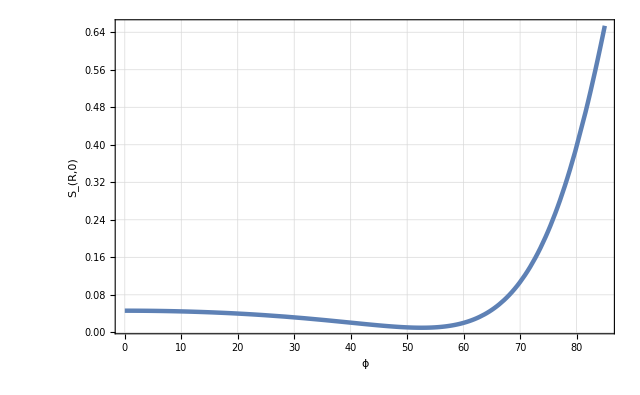

Stokes Vector R.

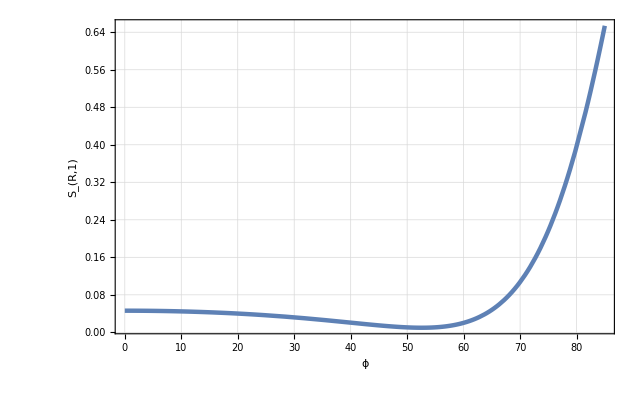

Stokes Vector R.

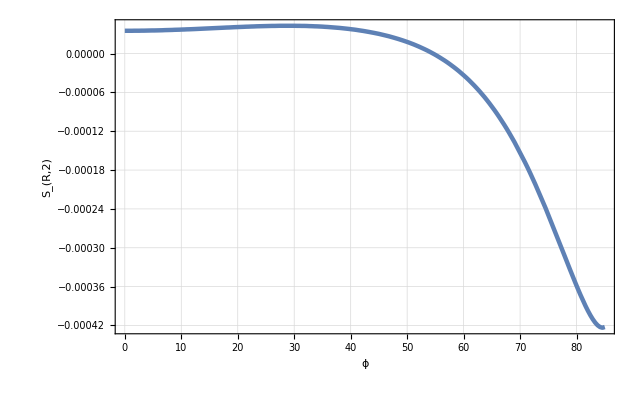

Stokes Vector R.

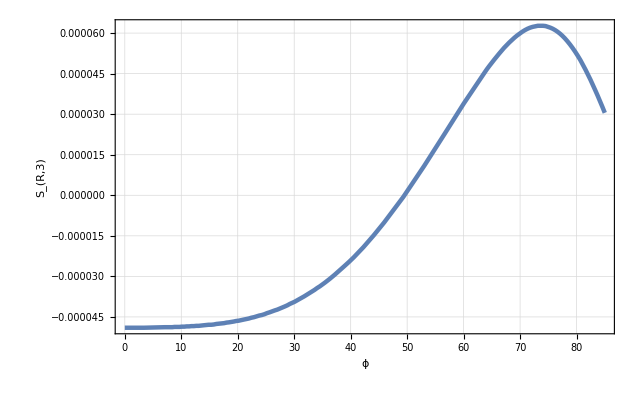

Full intensity of Reflected light.

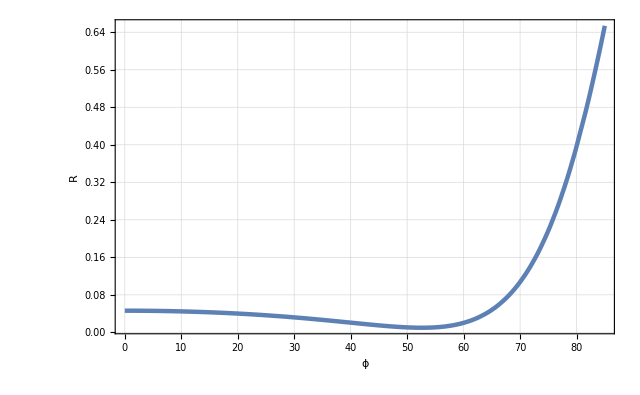

Full intensity of Transmitted light.

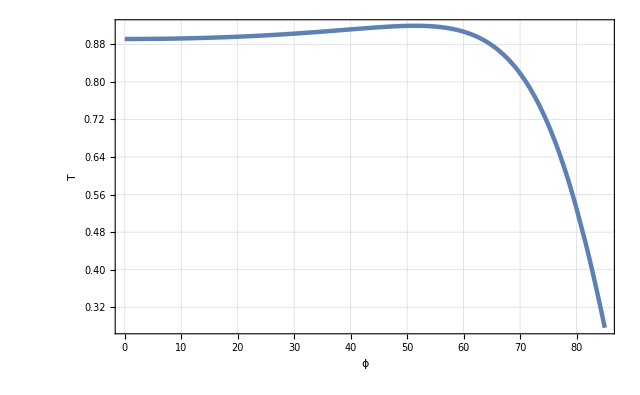

γ of Stokes Vector R.

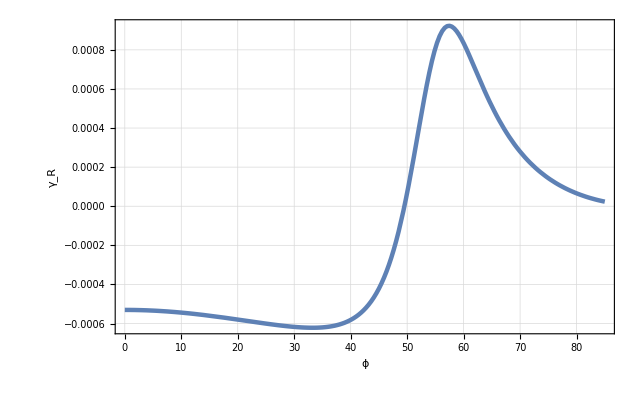

γ of Stokes Vector R (in degrees).

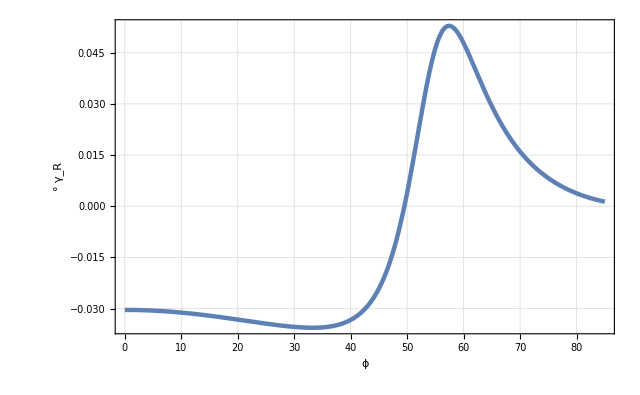

χ of Stokes Vector R.

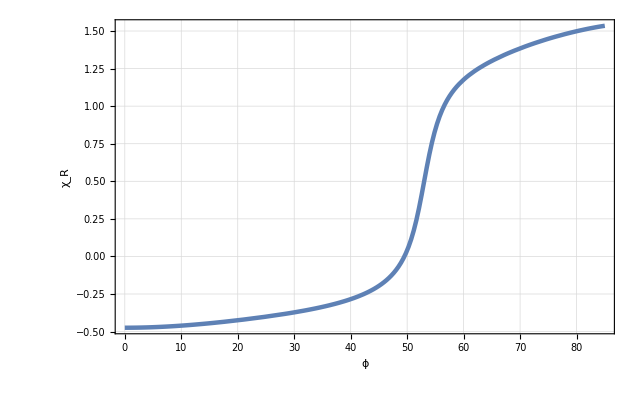

χ of Stokes Vector R (in degrees).

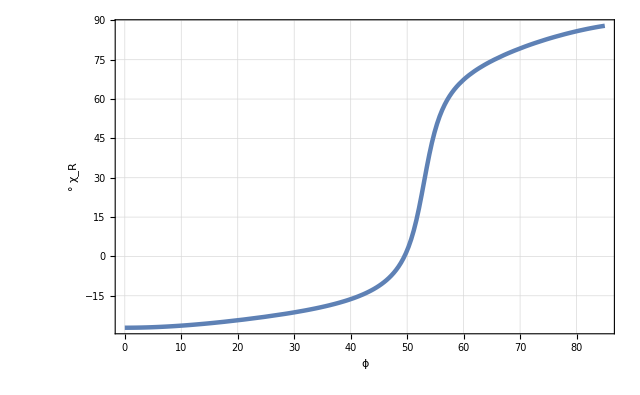

p of Stokes Vector R.

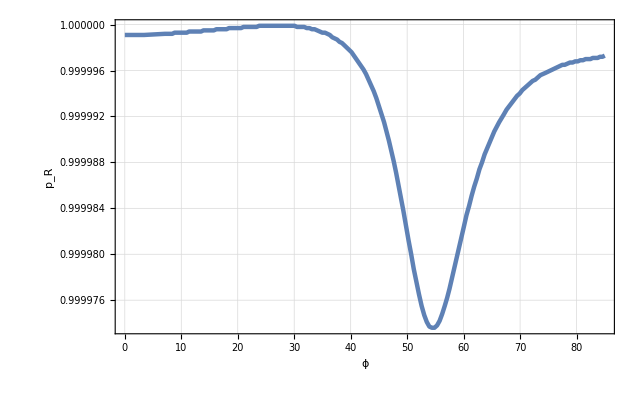

Azimuth of Reflected light in Degrees (new).

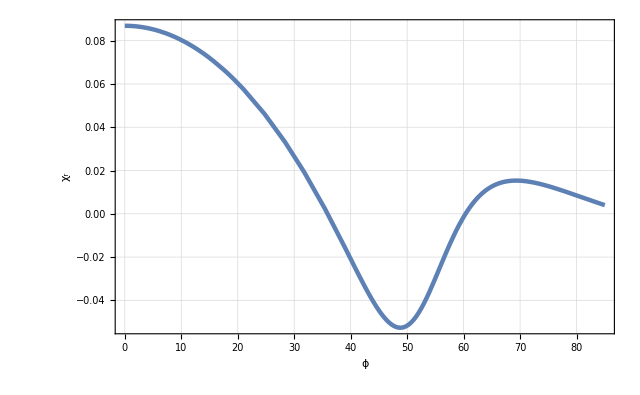

Ellipticity of Reflected light (new).

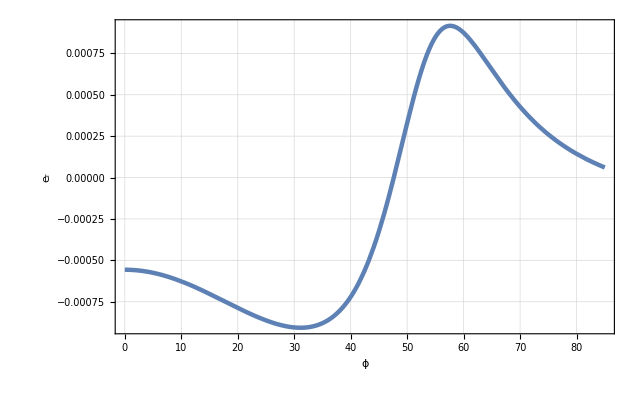

Psi pp in degrees.

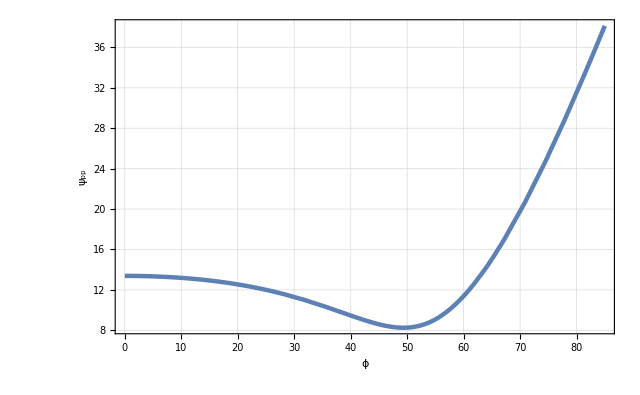

Delta pp in degrees.

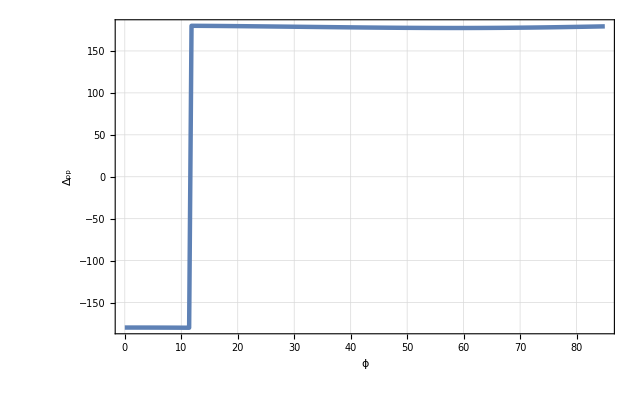

{Intensity of Reflected light going into X component.,Intensity of Reflected light going into Y component.}

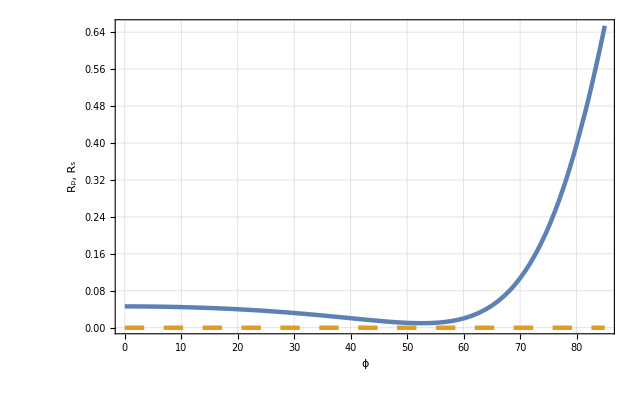

{Intensity of Transmitted light going into X component.,Intensity of Transmitted light going into Y component.}

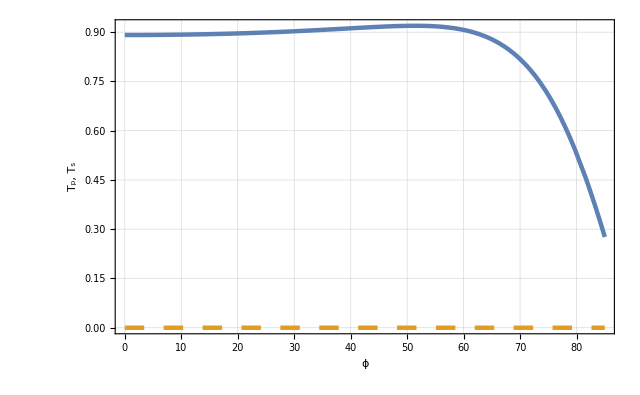

Tue 12 Apr 2016 20:03:46, time used: 2014, total time used: 2055.
---------------------------------------------

```mathematica
(* ============================================== *)
ClearAll["Global`*"];
(* ============================================== *)
PathList={"W:\\Math\\BM\\"};
BaseDir="W:\\Math\\BM\\";
BaseFileName="Example_08";
OutDir=BaseDir<>"Calc\\";
(* ============================================== *)
useParallelTbl=False;
Get["BerremanInit.m",Path-> PathList];
Initialize[PathList, useParallelTbl];
(* ============================================== *)
opts={BDPlotFigures -> True,UseEulerAngles->False};
(* ============================================== *)
(*
FuncList={{StokesVectorI[1],StokesVectorI[2],StokesVectorI[3],StokesVectorI[4]},{StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4]},{EltEG[1],EltEG[2],EltEG[3],EltEG[4]},{XitEGDegree[1],XitEGDegree[2],XitEGDegree[3],XitEGDegree[4]},{IFull,RFull,TFull},{Ix,Iy,Rx,Ry,Tx,Ty},{Eli,Elr,Elt},{XiiDegree, XirDegree,XitDegree},{Sin2Xii,Sin2Xir,Sin2Xit}};
*)

FuncList={StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4],RFull,TFull, StokesGammaR, StokesGammaDegreeR,StokesChiR, StokesChiDegreeR, StokesPolarizedR,XirDegree,Elr,PsiPPDegree,DeltaPPDegree,{Rx,Ry},{Tx,Ty}};

(* ============================================== *)
systemDescription="One Layer biaxial thin film on slighlty absorbing substrate plate.";
Print["!!! For absorbing plate I > R + T !!!"];
(* ============================================== *)
Print["Параметры падающего света..."];
nUpper=1; 

lambda={600,600,1,"λ",nm};fita={0,85,5,"ϕ", Degree};beta={0,90,45,"β", Degree};gamma={0, 0,30,"γ",Degree};
ellipt={0,0,0.5,"e"};

incidentLight=CreateIncidentRay[nUpper,lambda,fita,beta, ellipt];
OutputIncidentRayInfo[incidentLight];
(* ============================================== *)
Print["Оптические параметры первого тонкого слоя."];
thicknessLayer1={75,75,10,"h",nm};

fiLayer1={0, 0, 30,Subscript["φ","1"], Degree};thetaLayer1={0,0,30,Subscript["θ","1"],Degree};psiLayer1={0,0,30,Subscript["ψ","1"], Degree};
rotationAnglesLayer1={fiLayer1,thetaLayer1,psiLayer1};

epsLayer1=EpsilonFromN[1.50,2.00,1.75];
Print["epsLayer1 = ", epsLayer1 // MatrixForm];

layer1=CreateFilm[thicknessLayer1,rotationAnglesLayer1,epsLayer1];
(* ============================================== *)
Print["Оптические параметры второго тонкого слоя."];
thicknessLayer2={100,100,10,"h",nm};

fiLayer2={0, 0, 30,Subscript["φ","2"], Degree};thetaLayer2={0,0,30,Subscript["θ","2"],Degree};psiLayer2={0,0,30,Subscript["ψ","2"], Degree};
rotationAnglesLayer2={fiLayer2,thetaLayer2,psiLayer2};

epsLayer2=EpsilonFromN[1.75,1.50,2.00];
muLayer2=DiagonalMatrix[{1,1,1}];
rhoLayer2=I*{{1.9*10^-3,-3.5*10^-3,0},{3.5*10^-3,1.9*10^-3,0},{0,0,-5.7*10^-3}};
Print["epsLayer2 = ", epsLayer2 // MatrixForm];
Print["muLayer2 = ", muLayer2 // MatrixForm];
Print["rhoLayer2 = ", rhoLayer2 // MatrixForm];

layer2=CreateFilm[thicknessLayer2,rotationAnglesLayer2,epsLayer2,muLayer2,rhoLayer2];
(* ============================================== *)
Print["Оптические параметры толстой пластинки"];
Print["Для расчетов для различных толщин пластинки нужно поменять значение thickness"];
nSubstr=1.5;
kSubstr=3*10^-6;
thickness=1 mm;
thickPlate=CreateThickPlateFromN[thickness,nSubstr+I* kSubstr];
(* ============================================== *)
Print["Оптические параметры нижней среды..."];
nLower=1;
lowerMedia=CreateSemiInfiniteMediaFromN[nLower];
(* ============================================== *)
Print["Создаем оптическую систему..."];
layeredSystem = CreateLayeredSystem[incidentLight,gamma,layer1,layer2,thickPlate,lowerMedia];
OutputLayeredSystem[layeredSystem];
(* ============================================== *)
Print["Производим вычисления для различных значений параметров...."];
allCalc=PerformAllCalculations[layeredSystem,FuncList, systemDescription,opts];
(* ============================================== *)
```